```mathematica
update[x0_,y0_,z0_,k0_,l0_,phi0_]:=
{x0+1/k0*Tan[l0]*dphi,
y0+1/k0*(Cos[phi0+dphi]-Cos[phi0]),
z0+1/k0*(Sin[phi0+dphi]-Sin[phi0]),
k0,
l0,
phi0+dphi}
```

```mathematica
D[update[x,y,z,k,l,ϕ],{{x,y,z,k,l,ϕ}}]//MatrixForm
```

(1 | 0 | 0 | -(dphi Tan[l])/k^2 | (dphi Sec[l]^2)/k | 0
0 | 1 | 0 | -(-Cos[ϕ]+Cos[dphi+ϕ])/k^2 | 0 | (Sin[ϕ]-Sin[dphi+ϕ])/k
0 | 0 | 1 | -(-Sin[ϕ]+Sin[dphi+ϕ])/k^2 | 0 | (-Cos[ϕ]+Cos[dphi+ϕ])/k
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
updateWithTan[x0_,y0_,z0_,k0_,tanl0_,phi0_]:=
{x0+1/k0*tanl0*dphi,
y0+1/k0*(Cos[phi0+dphi]-Cos[phi0]),
z0+1/k0*(Sin[phi0+dphi]-Sin[phi0]),
k0,
tanl0,
phi0+dphi}
```

```mathematica
D[updateWithTan[x,y,z,k,tanl,ϕ],{{x,y,z,k,tanl,ϕ}}]//MatrixForm
```

(1 | 0 | 0 | -(dphi tanl)/k^2 | dphi/k | 0
0 | 1 | 0 | -(-Cos[ϕ]+Cos[dphi+ϕ])/k^2 | 0 | (Sin[ϕ]-Sin[dphi+ϕ])/k
0 | 0 | 1 | -(-Sin[ϕ]+Sin[dphi+ϕ])/k^2 | 0 | (-Cos[ϕ]+Cos[dphi+ϕ])/k
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

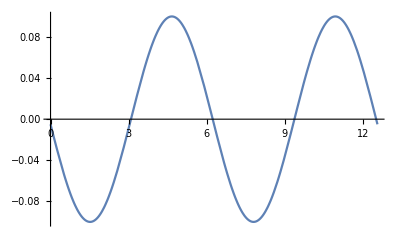

```mathematica
Plot[Cos[x+dx]-Cos[x]/.dx->0.1,{x,0,4Pi}]
```

```mathematica
updateCartesian[x_,y_,z_,px_,py_,pz_]:=
Flatten@Transpose[({{1, 0, 0, 1/m, 0, 0}, {0, 1, 0, 0, 1/m, 0}, {0, 0, 1, 0, 0, 1/m}, {0, 0, 0, 1, q/m*bz, -q/m*by}, {0, 0, 0, -q/m*bz, 1, q/m*bx}, {0, 0, 0, q/m*by, -q/m*bx, 1}}).({{x}, {y}, {z}, {px}, {py}, {pz}})+({{0}, {0}, {0}, {q ex}, {q ey}, {q ez}})]
```

```mathematica
updateCartesian[x,y,z,px,py,pz]
```

{px/m+x,py/m+y,pz/m+z,px+ex q+(bz py q)/m-(by pz q)/m,py+ey q-(bz px q)/m+(bx pz q)/m,pz+ez q+(by px q)/m-(bx py q)/m}

```mathematica
D[updateCartesian[x,y,z,px,py,pz],{{x,y,z,px,py,pz}}]//MatrixForm
```

(1 | 0 | 0 | 1/m | 0 | 0
0 | 1 | 0 | 0 | 1/m | 0
0 | 0 | 1 | 0 | 0 | 1/m
0 | 0 | 0 | 1 | (bz q)/m | -(by q)/m
0 | 0 | 0 | -(bz q)/m | 1 | (bx q)/m
0 | 0 | 0 | (by q)/m | -(bx q)/m | 1)